Transmon: Quantum Phase Model |

Transmon Hamiltonianpaclet:QuantumPlaybook/tutorial/TransmonQuantumPhaseModel#1938848208 | Bloch Statespaclet:QuantumPlaybook/tutorial/TransmonQuantumPhaseModel#428639651
Limiting Casespaclet:QuantumPlaybook/tutorial/TransmonQuantumPhaseModel#170388726 | Transmon Eigenstatespaclet:QuantumPlaybook/tutorial/TransmonQuantumPhaseModel#138156041

TransmonEnergypaclet:QuantumPlaybook/ref/TransmonEnergyQuantumPlaybook Package Symbol | Eigenenergy of the transmon Hamiltonian
TransmonFunctionpaclet:QuantumPlaybook/ref/TransmonFunctionQuantumPlaybook Package Symbol | Eigenfucntion of the transmon Hamiltonian
TransmonHamiltonianpaclet:QuantumPlaybook/ref/TransmonHamiltonianQuantumPlaybook Package Symbol | The Hamiltonian for a transmon

Functions to describe transmon physics.

The transmission-line shunted plasma oscillation qubit, or transmon in short, is a variant of superconducting charge qubit that is insensitive to charge noise. It consists of two small superconducting islands tunnel coupled through two Josephson junctions (forming a dc-SQUID) and shunted by a large capacitor (see Figure 1). The key feature that distinguishes the transmon from the so-called Cooper-pair box (Nakamura, Pashkin, and Tsai, 1999) is to reduce the sensitivity to charge noise using the capacitive shunt while maintaining a sufficient anharmonicity for selective  control of a pair of levels to form a quantum bit (Koch et al., 2007).

-Graphics-

Figure 1. A schematic of transmon. It consists of two superconducting islands tunnel coupled through two Josephson junctions and shunted by a large capacitor.

Load the Transmon package.

```mathematica
<<Transmon`
```

Transmon Hamiltonian

A transmon is a small Josephson junction and is described by the Hamiltonian

,

where  is the charging energy associated with junction capacitance ,  is the Josephson energy, and  is the dimensionless gate charge for gate capacitance  and voltage   (see Figure 2). Two operators  and  describe the number of Cooper pairs and the phase of the superconducting order parameter, respectively. The two operators  and  satisfy the commutation relation

.

Due to this commutation relation, the phase and number are subjected to quantum fluctuations satisfying the uncertainty relation

.

In this sense, the above transmon Hamiltonian is also called the quantum phase model.

-Graphics-

Figure 2. An equivalent circuit for transmon. A transmon is a small Josephson junction characterized by Josephson critical current   and shunted by a large capacitance . The Josephson critical current  determines the Josephson energy  while the capacitance  gives the charging energy scale . The transmon device is often tuned by an external gate voltage via a gate capacitor of capacitance , inducing the dimensionless gate charge .

The quantum fluctuations of the phase and number are governed by the two energy scales and  in the transmon Hamiltonian. If , then the first term dominates, and the number is well defined while the phase strongly fluctuates. In the opposite limit, , the Josephson term dominates and the phase is well defined whereas the Cooper-pair number has a large uncertainty. It is thus convenient to characterize the quantum fluctuations with the ratio of the two energy scales, more precisely, with

.

which is called the MacCumber parameter of the transmon device. Furthermore, we measure energies in units of the geometric mean of the two energy scales, that is,

.

Then, the dimensionless transmon Hamiltonian reads as

.

In the ϕ-space representation, the corresponding Schrödinger equation is given by

,	.

Phases 0 and 2π are equivalent, so physically meaningful wave function must satisfy the periodic boundary condition

.

Limiting Cases

```mathematica
<<Transmon`
```

### Charging Limit ()

(under construction)

### Josephson Limit ()

(under construction)

Bloch States

BlochEnergypaclet:QuantumPlaybook/ref/BlochEnergyQuantumPlaybook Package Symbol | The energy of a Bloch state for a characteristic exponent
BlochFunctionpaclet:QuantumPlaybook/ref/BlochFunctionQuantumPlaybook Package Symbol | The wave function of a Bloch state for a characteristic exponent

Functions related to Bloch states.

```mathematica
<<Transmon`
```

Here, we consider a slightly different model described by the Hamiltonian

and the open boundary condition (instead of the periodic boundary condition). In the ϕ-space representation, the Schrödinger equation reads as

.

We call the above Hamiltonian the Mathieu Hamiltonian and the model consisting of the Mathieu Hamiltonian (or equivalently the Mathieu-Schrödinger equation) with the open boundary condition the Mathieu model.

Notice the absence of the dimensionless gate charge  from this Hamiltonian (cf. the above specification of the transmon Hamiltonian or the corresponding Schrödinger equation). Without the periodic boundary condition, the dimensionless gate charge  can always be "gauged away". To see this, assume a solution of the form  in the Schrödinger equation with finite . Then, one can see that  satisfies the above Mathieu-Schrödinger equation without .

### Bloch Theorem

Note that the Hamiltonian has a discrete translational symmetry. More specifically, let  be the translation operator by amount θ such that

.

The Hamiltonian commutes with any translation by integer multiples of 2π,

for every integer .

According to the Bloch (or Floquet) theorem, the discrete translational symmetry allows us to choose eigenstates of the Hamiltonian of the form

,

where  is a periodic function of period 2π and real parameter ν is called the characteristic exponent (or the quasi-momentum) of the wave function. A state with wave function of the above form is called a Bloch (or Floquet) states.

Consider an eigenfunction with a specific characteristic exponent.

```mathematica
α=2.;
ν=1.25;
sol[x_]=BlochFunction[ν,α,x];
```

The wave function itself is not periodic due to the non-integer value of the characteristic exponent.

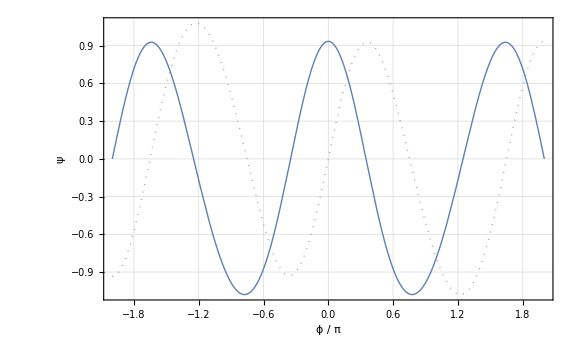

```mathematica
ReImPlot[sol[x*Pi],{x,-2,2},
FrameLabel->{"ϕ / π","ψ"}]
```

However, with the plane-wave factor removed, the remaining part is periodic.

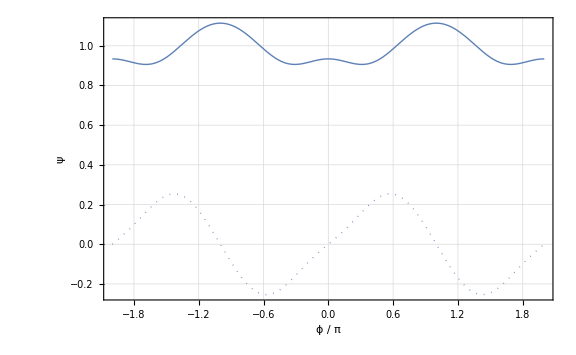

```mathematica
ReImPlot[Exp[-I*ν*x*Pi]*sol[x*Pi],{x,-2,2},
FrameLabel->{"ϕ / π","ψ"}]
```

The energy depends on the characteristic exponent. The dispersion relation forms bands.

Here is an example of the dispersion relation in the charging limit. The dispersion relation resembles a quadratic curve.

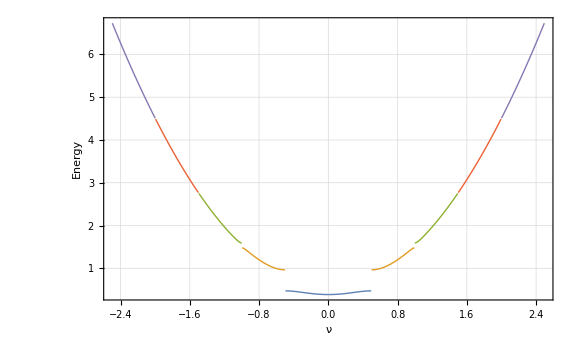

```mathematica
α=2.;
d=0.005;
fig1a=ListPlot[
Table[{n+nu,BlochEnergy[n+nu,α]},{n,0,2,1/2},{nu,0,0.5-d,d}],
Joined->True];
fig1b=ListPlot[
Table[{n+nu,BlochEnergy[n+nu,α]},{n,0,-2,-1/2},{nu,0,-0.5+d,-d}],
Joined->True];
fig1=Show[{fig1a,fig1b},FrameLabel->{"ν","Energy"},PlotRange->All]
```

Here is an example of the dispersion relation in the Josephson limit. The allowed values of energy are almost discrete and are similar to those of simple harmonic oscillator.

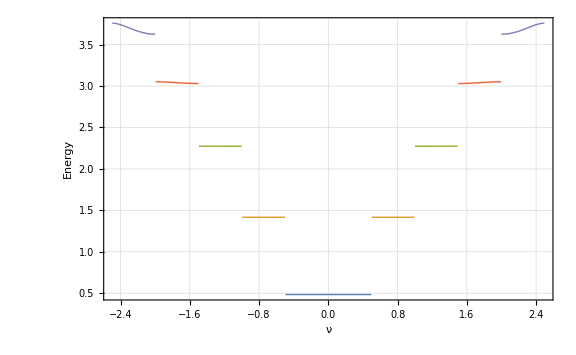

```mathematica
α=0.5;
d=0.005;
fig2a=ListPlot[
Table[{n+nu,BlochEnergy[n+nu,α]},{n,0,2,1/2},{nu,0,0.5-d,d}],
Joined->True];
fig2b=ListPlot[
Table[{n+nu,BlochEnergy[n+nu,α]},{n,0,-2,-1/2},{nu,0,-0.5+d,-d}],
Joined->True];
fig2=Show[{fig2a,fig2b},FrameLabel->{"ν","Energy"},PlotRange->All]
```

### Mathieu Functions

The Bloch Hamiltonian has additional symmetry. That is, it is invariant under parity  (i.e., space inversion):   and . Therefore, it is possible to choose simultaneous eigenstates of the Hamiltonian and parity. However, the Bloch states of the form  do not have a definite parity; that is, they are not eigenstates of the parity operator. Nevertheless, it is possible to construct simultaneous eigenstates of the Hamiltonian and parity by starting with the Bloch states.

We first note that if  is a solution of the Schrödinger equation, then   is also a solution to the same Schrödinger equation with the same energy . Therefore, the two functions defined by

are also solutions to the same Schrödinger equation with the same energy. Moreover, it turns out that unless   is an integer (ν is a half-integer),  and  are linearly independent. This means that the two functions  and  are also linearly independent. Therefore, since they are manifestly eigenstates of the parity operator (with opposite parities), they are the desired wave functions.  These functions are called the Mathieu cosine and sine functions, respectively, with characteristic exponent  and are solutions to the Mathieu equations

,

where  and . Putting it another way, one can find the Bloch states starting from the Mathieu functions,

.

For integer ,  and  are proportional to each other. In this case, either of the Mathieu functions  or  is an eigenstate and is both a Bloch state and parity eigenstate.

Transmon Eigenstates

```mathematica
<<Transmon`
```

Let us get back to the original problem with the Schrödinger equation (corresponding to the transmon Hamiltonian) and periodic boundary condition. Let . Clearly, it satisfies the Schrödinger equation

.

Moreover, since the physical wave function satisfy the periodic boundary condition , the fictitious wave function  is a Bloch wave function with characteristic exponent  for arbitrary integer m.

In short, eigenstates of the transmon Hamiltonian has energy

and wave function

,

where  is the characteristic value of the parameter a in the Mathieu equation with parameter g that leads to the Mathieu characteristic exponent  .

As an example, consider the first excited state of the transmon Hamiltonian.

```mathematica
n=1;
α=2.0;
q=0.25;
sol[x_]=TransmonFunction[n,α,q,x]//Simplify;
```

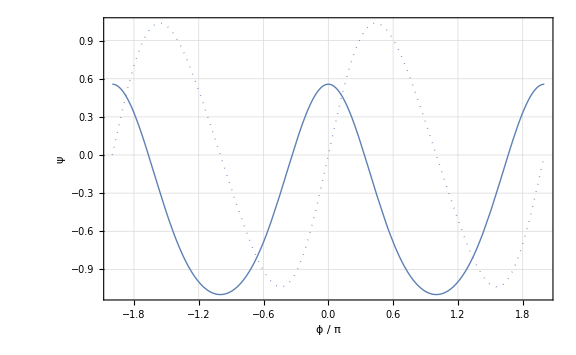

```mathematica
ReImPlot[sol[x*Pi],{x,-2,2},PlotRange->All,
FrameLabel->{"ϕ / π", "ψ"}]
```

Clearly, the above wave function satisfies the Schrödinger equation.

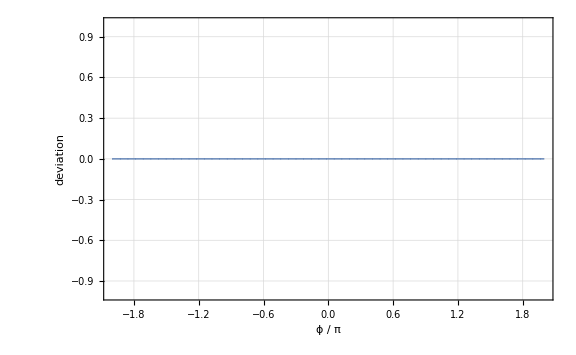

```mathematica
eqn[x_]=TransmonHamiltonian[α,q,x]@sol[x]-TransmonEnergy[n,α,q]*sol[x]//Simplify;
ReImPlot[eqn[x*Pi],{x,-2,2},PlotRange->All,FrameLabel->{"ϕ / π", "deviation"}]
```

Consider another example in the opposite limit.

```mathematica
n=1;
α=0.5;
q=0.25;
sol[x_]=TransmonFunction[n,α,q,x]//Simplify;
```

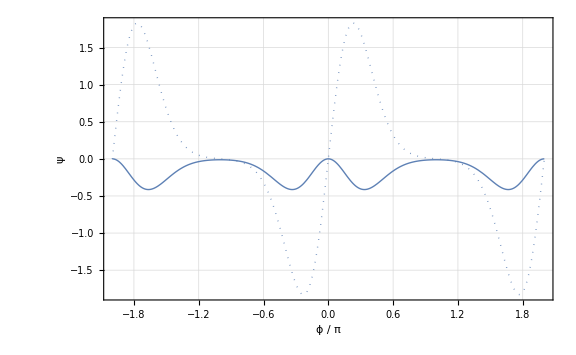

```mathematica
ReImPlot[sol[x*Pi],{x,-2,2},PlotRange->All,
FrameLabel->{"ϕ / π", "ψ"}]
```

```mathematica
eqn[x_]=TransmonHamiltonian[α,q,x]@sol[x]-TransmonEnergy[n,α,q]*sol[x]//Simplify;
ReImPlot[eqn[x*Pi],{x,-2,2},PlotRange->All,FrameLabel->{"ϕ / π", "deviation"}]
```

-Graphics-

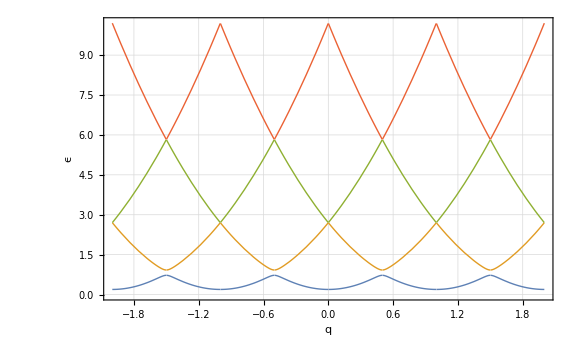

```mathematica
Clear[q];
α=5.0;
Plot[Evaluate@Table[TransmonEnergy[k,α,q],{k,0,3}],{q,-2,2},
FrameLabel->{"q","ϵ"}]
```

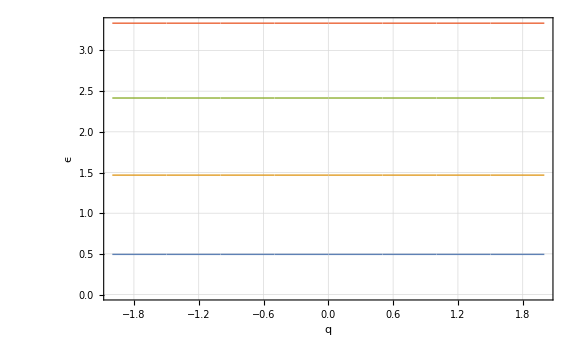

```mathematica
Clear[q];
α=0.2;
Plot[Evaluate@Table[TransmonEnergy[k,α,q],{k,0,3}],{q,-2,2},
FrameLabel->{"q","ϵ"}]
```

As the MacCumber parameter α varies, the spectrum gradually changes from the Josephson to charging limit.

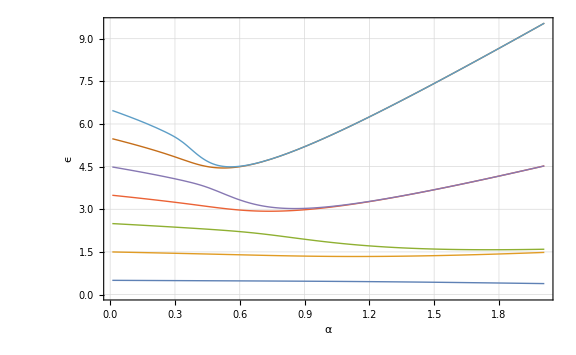

```mathematica
Plot[
Evaluate@Table[TransmonEnergy[n,alpha,0],{n,0,6}],{alpha,0.01,2.01},
FrameLabel->{"α","ϵ"}
]
```

The degeneracy in the Josephson limit is lifted for finite dimensionless gate charge q.

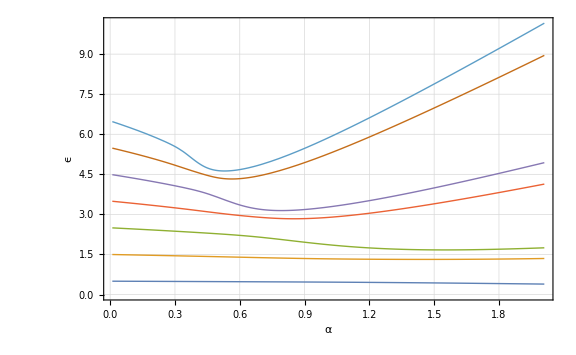

```mathematica
Plot[
Evaluate@Table[TransmonEnergy[n,alpha,0.1],{n,0,6}],{alpha,0.01,2.01},
FrameLabel->{"α","ϵ"}
]
```

| Related Guides
▪Quantum Information Systems
▪Quantum Many-Body Systems
▪Quantum Spin Systems

| Related Tech Notes
▪A Quantum Playbook
▪Mathieu and Related Functions
▪Quantum Information Systems with Q3

| Related Links
▪Y. Nakamura, Y. A. Pashkin, and J. S. Tsai, Nature 398, 786 (1999)https://doi.org/10.1038/19718, "Coherent control of macroscopic quantum states in a single-Cooper-pair box."
▪J. Koch https://doi.org/10.1103/PhysRevA.76.042319et al., Physical Review A 76, 042319 (2007)https://doi.org/10.1103/PhysRevA.76.042319, "Charge-insensitive qubit design derived from the Cooper pair box."
▪G. Blanch (1972)https://dlmf.nist.gov/28, "Mathieu Functions" in Handbook of Mathematical Functions with Formulas, Graphs, and Mathematical Tables, edited by M. Abramowitz and I. A. Stegun (John Wiley & Sons, 1972).